```mathematica
StringToSet[s_]:=Block[{result},
Table[FromDigits[StringTake[s,{k}]],{k,1,StringLength[s]}]
]
```

```mathematica
StringToSet["1234"]
```

{1,2,3,4}

```mathematica
ApplySolution[g_,symbol_]:=Block[{blocks,edges={},vertices,h},
blocks=StringSplit[ StringDrop[SymbolName[symbol],1],"x"];
Table[
vertices=StringToSet[b];
Table[edges=Append[edges,s[[1]]<->s[[2]]],{s,Subsets[vertices,{2}]}]
,{b,Select[blocks,StringLength[#]>1&]}
];
h=EdgeAdd[g,edges];
Graph[h,GraphHighlight->edges, GraphHighlightStyle->"Thick"]
]
```

```mathematica
SymbolToKey2[s_]:=Block[{tail=StringDrop[s,1], temp},
temp=ToExpression[tail];
If[!NumericQ[temp],
tail,
temp]
]
```

```mathematica
SetComp[s1_,s2_]:=Block[{l=Min[Length[s1],Length[s2]],i},
For[i=1,i≤l,i++,
If[s1[[i]]≠s2[[i]],
Return[s1[[i]]>s2[[i]]]
]
];
Return[Length[s1]>Length[s2]]
]
```

```mathematica
SymbolComp3[x_,y_]:=Block[{n1=SymbolName[x],n2=SymbolName[y],a,b,h1,h2,l1,l2},
h1=StringDrop[n1,1];
h2=StringDrop[n2,1];
l1=Sort[Map[StringLength[#]&,StringSplit[h1,"x"]],Greater];
l2=Sort[Map[StringLength[#]&,StringSplit[h2,"x"]],Greater];
Return[SetComp[l1,l2]]
]
```

```mathematica
allGraphs5FakeAtomKeys=Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofournull"]]]==1&];Length[allGraphs5FakeAtomKeys]
```

52

```mathematica
Table[allGraphs5[k,"graph"],{k,allGraphs5FakeAtomKeys}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
repFake5=Table[allGraphs5[k,"colofournull"]->allGraphs5[k,"graph"],{k,allGraphs5FakeAtomKeys}];
```

```mathematica
Table[Framed[Labeled[allGraphs5[k,"graph"],Style[k,Red]]->Column[{Table[ApplySolution[allGraphs5[k,"graph"],symb],{symb,Sort[ListofVars[allGraphs5[k,"colofour"]],SymbolComp3[#1,#2]&]}],Framed[allGraphs5[k,"colofournull"]/.repFake5]}]],{k,RandomSample[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&],10]}]//TableForm
```

-Graphics-22144→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
1/12 (-2 -Graphics-+2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics-+2 -Graphics-+4 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics--4 -Graphics-+4 -Graphics-+2 -Graphics--4 -Graphics-+2 -Graphics--2 -Graphics-+2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics-+3 -Graphics-+3 -Graphics--3 -Graphics-+3 -Graphics--3 -Graphics--3 -Graphics--3 -Graphics-+3 -Graphics-+9 -Graphics--3 -Graphics---Graphics-+-Graphics-+3 -Graphics---Graphics-+-Graphics-+3 -Graphics-)
-Graphics-4→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
1/2 (--Graphics-+-Graphics-+-Graphics-+-Graphics-)
-Graphics-22935→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
1/12 (-2 -Graphics-+2 -Graphics-+2 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics--4 -Graphics-+4 -Graphics-+4 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics--5 -Graphics-+7 -Graphics-+-Graphics-+-Graphics--5 -Graphics-+-Graphics--5 -Graphics-+-Graphics-+-Graphics-+7 -Graphics-+3 -Graphics-+-Graphics---Graphics-+-Graphics---Graphics-+5 -Graphics-)
-Graphics-364→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-
-Graphics-6841→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
1/24 (-2 -Graphics-+6 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics-+2 -Graphics-+2 -Graphics--6 -Graphics--10 -Graphics-+2 -Graphics-+2 -Graphics-+2 -Graphics--6 -Graphics-+2 -Graphics-+2 -Graphics-+6 -Graphics-+2 -Graphics-+6 -Graphics--6 -Graphics-+6 -Graphics--2 -Graphics-+2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics-+2 -Graphics-+2 -Graphics--6 -Graphics-+2 -Graphics-+9 -Graphics--3 -Graphics--3 -Graphics--3 -Graphics-+9 -Graphics--3 -Graphics-+9 -Graphics--3 -Graphics--3 -Graphics--3 -Graphics-+-Graphics-+-Graphics--3 -Graphics-+-Graphics-+9 -Graphics-+3 -Graphics-)
-Graphics-29515→{-Graphics-,-Graphics-}
1/12 (-2 -Graphics-+2 -Graphics-+2 -Graphics--2 -Graphics-+2 -Graphics-+2 -Graphics--2 -Graphics--6 -Graphics-+2 -Graphics-+2 -Graphics-+4 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics-+4 -Graphics--2 -Graphics--2 -Graphics-+4 -Graphics--2 -Graphics--2 -Graphics-+6 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics-+3 -Graphics-+3 -Graphics--9 -Graphics--3 -Graphics--3 -Graphics-+3 -Graphics-+3 -Graphics-+3 -Graphics-+3 -Graphics--3 -Graphics---Graphics-+3 -Graphics-+3 -Graphics---Graphics---Graphics-+9 -Graphics-)
-Graphics-28683→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
1/6 (--Graphics-+2 -Graphics---Graphics---Graphics-+2 -Graphics---Graphics-+2 -Graphics--4 -Graphics-+2 -Graphics-+2 -Graphics---Graphics-+2 -Graphics---Graphics-+4 -Graphics-)
-Graphics-26982→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
1/24 (-2 -Graphics-+6 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics-+10 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics-+10 -Graphics-+2 -Graphics-+2 -Graphics--10 -Graphics-+6 -Graphics--2 -Graphics--2 -Graphics-+6 -Graphics-+6 -Graphics--2 -Graphics--2 -Graphics--2 -Graphics-+2 -Graphics--2 -Graphics---Graphics---Graphics-+11 -Graphics---Graphics---Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+3 -Graphics-+3 -Graphics---Graphics-+3 -Graphics---Graphics-+-Graphics-)
-Graphics-19686→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-
-Graphics-6670→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-

```mathematica
Table[allGraphs6[k,"graph"]->Table[ApplySolution[allGraphs6[k,"graph"],symb],{symb,ListofVars[allGraphs6[k,"colofour"]]}],{k,Take[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&],5]}]//TableForm
```

-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

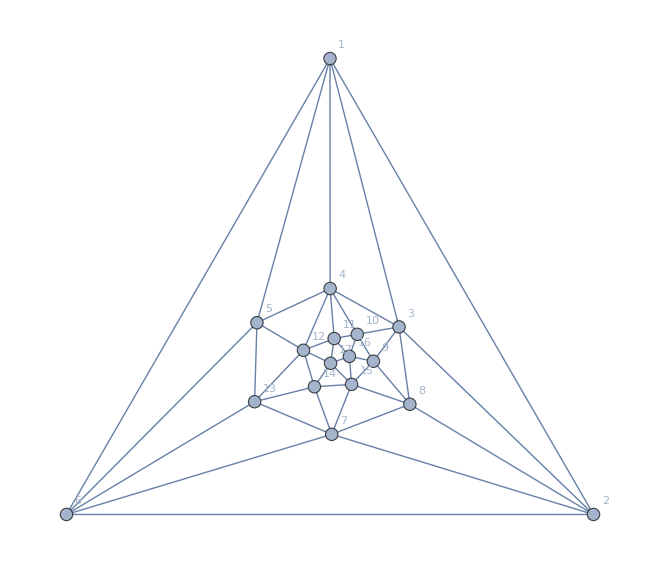

```mathematica
Graph[plantri[[8]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```